```mathematica
a={3,3,-4,1};
b={5,3,-4,1};
c={5,5,-4,1};
d={3,5,-4,1};
aPrime={3,3,-6,1};
bPrime={5,3,-6,1};
cPrime={5,5,-6,1};
dPrime={3,5,-6,1};
d2Prime={8,8,-6,1};

(*a={30,30,-15,1};
b={15,11,-15,1};
c={5,51,-15,1};
d={15,5,-10,1};
e={32,3,-61,1};
f={15,31,-15,1};
g={10,11,-16,1};
h={38,59,-61,1};
i={8,80,-65,1};*)

Oc={0,0,0,1};
Oc2={5,0,2,1};
zeta1 = 2;
zeta2=1;
alpha=45;
beta = 0;
Rot1=RotationsE2[alpha];
Rot2=RotationsE2[beta];
```

```mathematica
ClearAll["Global`*"];
```

OC2 = {5,0,2,1}

M of C2=(1/(√2) | 0 | -1/(√2) | -3/(√2)
0 | 1 | 0 | 0
1/(√2) | 0 | 1/(√2) | -7/(√2)
0 | 0 | 0 | 1)

M2 of C1 =(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1)

ProjectionMtxCamera1(2 | 0 | 0 | 0
0 | 2 | 0 | 0
0 | 0 | 2 | 0
0 | 0 | 1 | 0)

ProjectionMtxCamera2(1/(√2) | 0 | -1/(√2) | -5/(√2)+√2
0 | 1 | 0 | 0
1/(√2) | 0 | 1/(√2) | -5/(√2)-√2
1/(√2) | 0 | 1/(√2) | -5/(√2)-√2)

CameraProjectedPointsK1 = (6 | 6 | -8 | -4
10 | 6 | -8 | -4
10 | 10 | -8 | -4
6 | 10 | -8 | -4
6 | 6 | -12 | -6
10 | 6 | -12 | -6
10 | 10 | -12 | -6
6 | 10 | -12 | -6
16 | 16 | -12 | -6)

CameraProjectedPointsK2 = (2 √2 | 3 | -4 √2 | -4 √2
3 √2 | 3 | -3 √2 | -3 √2
3 √2 | 5 | -3 √2 | -3 √2
2 √2 | 5 | -4 √2 | -4 √2
3 √2 | 3 | -5 √2 | -5 √2
4 √2 | 3 | -4 √2 | -4 √2
4 √2 | 5 | -4 √2 | -4 √2
3 √2 | 5 | -5 √2 | -5 √2
11/(√2) | 8 | -5/(√2) | -5/(√2))

homogene CameraProjectedPointsK1 = (-3/2 | -3/2 | 2 | 1
-5/2 | -3/2 | 2 | 1
-5/2 | -5/2 | 2 | 1
-3/2 | -5/2 | 2 | 1
-1 | -1 | 2 | 1
-5/3 | -1 | 2 | 1
-5/3 | -5/3 | 2 | 1
-1 | -5/3 | 2 | 1
-8/3 | -8/3 | 2 | 1)

homogene CameraProjectedPointsK2 = (-1/2 | -3/(4 √2) | 1 | 1
-1 | -1/(√2) | 1 | 1
-1 | -5/(3 √2) | 1 | 1
-1/2 | -5/(4 √2) | 1 | 1
-3/5 | -3/(5 √2) | 1 | 1
-1 | -3/(4 √2) | 1 | 1
-1 | -5/(4 √2) | 1 | 1
-3/5 | -1/(√2) | 1 | 1
-11/5 | -(8 √2)/5 | 1 | 1)

Begin construct Epipol_______________________________________________

End construct Epipol_______________________________________________

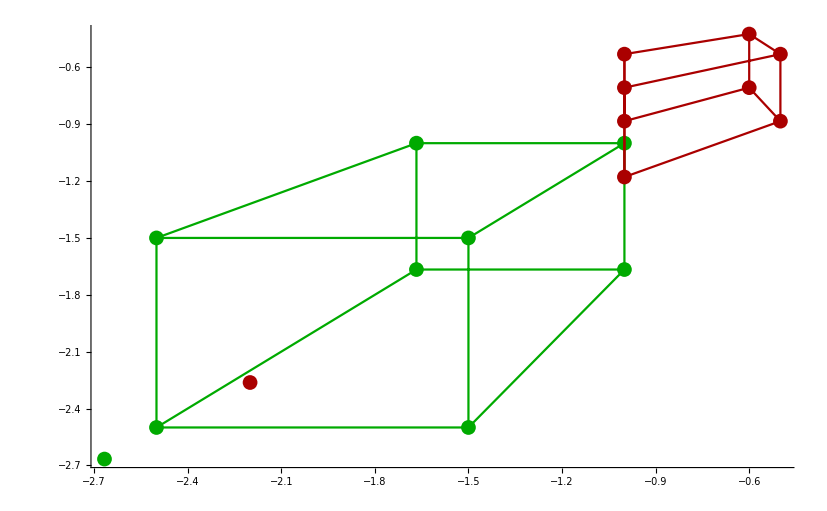

ImagePlaneC1Points = (-3/2 | -3/2 | 1
-5/2 | -3/2 | 1
-5/2 | -5/2 | 1
-3/2 | -5/2 | 1
-1 | -1 | 1
-5/3 | -1 | 1
-5/3 | -5/3 | 1
-1 | -5/3 | 1
-8/3 | -8/3 | 1)

ImagePlaneC2Points = (-1/2 | -3/(4 √2) | 1
-1 | -1/(√2) | 1
-1 | -5/(3 √2) | 1
-1/2 | -5/(4 √2) | 1
-3/5 | -3/(5 √2) | 1
-1 | -3/(4 √2) | 1
-1 | -5/(4 √2) | 1
-3/5 | -1/(√2) | 1
-11/5 | -(8 √2)/5 | 1)

CoefficientMtx = (3/4 | 3/4 | -1/2 | 9/(8 √2) | 9/(8 √2) | -3/(4 √2) | -3/2 | -3/2 | 1
5/2 | 3/2 | -1 | 5/(2 √2) | 3/(2 √2) | -1/(√2) | -5/2 | -3/2 | 1
5/2 | 5/2 | -1 | 25/(6 √2) | 25/(6 √2) | -5/(3 √2) | -5/2 | -5/2 | 1
3/4 | 5/4 | -1/2 | 15/(8 √2) | 25/(8 √2) | -5/(4 √2) | -3/2 | -5/2 | 1
3/5 | 3/5 | -3/5 | 3/(5 √2) | 3/(5 √2) | -3/(5 √2) | -1 | -1 | 1
5/3 | 1 | -1 | 5/(4 √2) | 3/(4 √2) | -3/(4 √2) | -5/3 | -1 | 1
5/3 | 5/3 | -1 | 25/(12 √2) | 25/(12 √2) | -5/(4 √2) | -5/3 | -5/3 | 1
3/5 | 1 | -3/5 | 1/(√2) | 5/(3 √2) | -1/(√2) | -1 | -5/3 | 1
88/15 | 88/15 | -11/5 | (64 √2)/15 | (64 √2)/15 | -(8 √2)/5 | -8/3 | -8/3 | 1)

RowReduce CoefficientMtx = [(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 7/3 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | -(2 √2)/3 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | (10 √2)/3 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)]

ns ={{0,-7/3,0,(2 √2)/3,0,-(10 √2)/3,0,1,0}}

F = (0. | -2.33333 | 0.
0.942809 | 0. | -4.71405
0. | 1. | 0.)

lC1 = {{3.5,-6.12826,-1.5},{3.5,-7.07107,-1.5},{5.83333,-7.07107,-2.5},{5.83333,-6.12826,-2.5},{2.33333,-5.65685,-1.},{2.33333,-6.28539,-1.},{3.88889,-6.28539,-1.66667},{3.88889,-5.65685,-1.66667},{6.22222,-7.2282,-2.66667}}

lPrimeC1 = {{-0.5,2.16667,2.5},{-0.666667,3.33333,3.33333},{-1.11111,3.33333,5.55556},{-0.833333,2.16667,4.16667},{-0.4,2.4,2.},{-0.5,3.33333,2.5},{-0.833333,3.33333,4.16667},{-0.666667,2.4,3.33333},{-2.13333,6.13333,10.6667}}

e = {5,0,1}

e' = {3/7,0,1}

EpipoleLines = (-7/3 | (26 √2)/9 | 1
-7/3 | (10 √2)/3 | 1
-7/3 | 2 √2 | 1
-7/3 | (26 √2)/15 | 1
-7/3 | 4 √2 | 1
-7/3 | (40 √2)/9 | 1
-7/3 | (8 √2)/3 | 1
-7/3 | (12 √2)/5 | 1
-7/3 | 23/(6 √2) | 1)

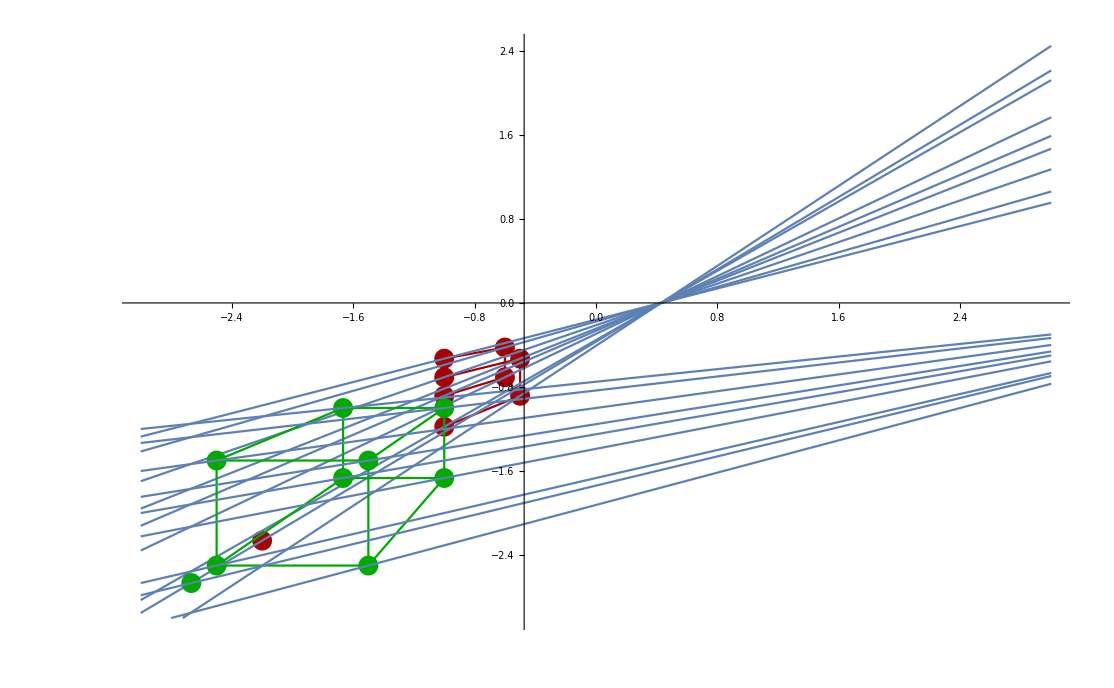

Begin Computing essential Matrix___________________________________________________

EMtx = {{0,-7/(5 √2),0},{2/5,0,1},{0,-3/(5 √2),0}}

U of E = {{0.,-0.919145,-0.393919},{1.,0.,0.},{0.,-0.393919,0.919145}}

Sigma of E = {{1.07703,0.,0.},{0.,1.07703,0.},{0.,0.,0.}}

V of E = {{0.371391,0.,-0.928477},{0.,1.,0.},{0.928477,0.,0.371391}}

S1 = (0. | -0.919145 | 0.
0.919145 | 0. | 0.393919
0. | -0.393919 | 0.)

S2 = (0. | 0.919145 | 0.
-0.919145 | 0. | -0.393919
0. | 0.393919 | 0.)

R1 = (0.707107 | 0. | 0.707107
0. | 1. | 0.
-0.707107 | 0. | 0.707107)

R2 = (0.024383 | 0. | -0.999703
0. | -1. | 0.
-0.999703 | 0. | -0.024383)

t = {-0.393919,0.,0.919145}

P21  = (0.024383 | 0. | -0.999703 | 0.393919
0. | -1. | 0. | 0.
-0.999703 | 0. | -0.024383 | -0.919145)

P22  = (0.707107 | 0. | 0.707107 | 0.393919
0. | 1. | 0. | 0.
-0.707107 | 0. | 0.707107 | -0.919145)

P23  = (0.024383 | 0. | -0.999703 | -0.393919
0. | -1. | 0. | 0.
-0.999703 | 0. | -0.024383 | 0.919145)

P24  = (0.707107 | 0. | 0.707107 | -0.393919
0. | 1. | 0. | 0.
-0.707107 | 0. | 0.707107 | 0.919145)

End Computing essential Matrix___________________________________________________

```mathematica
StartComputation[];
```